```mathematica
(* speed of light *)
c=2.998*10^8;
(* frequency of red light in Hz *)
fRED= c/(750*10^-9);
fVIOLET= c/(380*10^-9);
(* brightness parameter *)
k=680;
(* setting the key to be 2 and red *)
f0=fRED;
base=11;
```

```mathematica
SetDirectory["/Users/jackson/Documents/GitHub/synesthesiaer"];
```

```mathematica
{λ,x,y,z}=Import["http://www.cvrl.org/database/data/cmfs/ciexyzjv.csv"]ᵀ;
(*convert λ to m*)
λ=10^-9*λ;
```

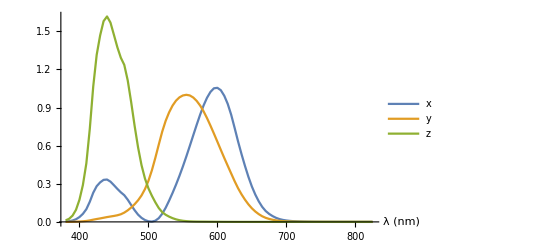

```mathematica
ListLinePlot[{{10^9*λ,x}ᵀ,{10^9*λ,y}ᵀ,{10^9*λ,z}ᵀ},PlotLegends->{"x","y","z"},AxesLabel->{"λ (nm)"}]
```

```mathematica
xtable=Table[{λ[[i]],x[[i]]},{i,1,Length[λ]}];
ytable=Table[{λ[[i]],y[[i]]},{i,1,Length[λ]}];
ztable=Table[{λ[[i]],z[[i]]},{i,1,Length[λ]}];
```

```mathematica
xbar=Interpolation[xtable];
ybar=Interpolation[ytable];
zbar=Interpolation[ztable];
```

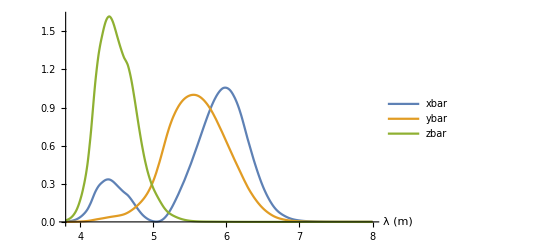

```mathematica
Plot[{xbar[λ],ybar[λ],zbar[λ]},{λ,380*10^-9,800*10^-9},PlotLegends->{"xbar","ybar","zbar"},AxesLabel->{"λ (m)"}]
```

```mathematica
(* frequency associated to a prime number *)
f[b_,p_]:=f0*Log[b,p]
```

```mathematica
(* perform convolution of power spectrum with color matching functions to obtain XYZ color values *)
XYZ[n_]:=Module[{fac=FactorInteger[n],X,Y,Z},
X=k*Sum[fac[[i,2]]*xbar[ c/f[base,fac[[i,1]]] ],{i,1,Length[fac]}];
Y=k*Sum[fac[[i,2]]*ybar[c/f[base,fac[[i,1]]] ],{i,1,Length[fac]}];
Z=k*Sum[fac[[i,2]]*zbar[c/f[base,fac[[i,1]]] ],{i,1,Length[fac]}];
Return[{X,Y,Z}]
]
```

```mathematica
(* assigns a color to a number in a natural way *)
Color[n_]:=ColorConvert[XYZColor@@XYZ[n],"RGB"]
```

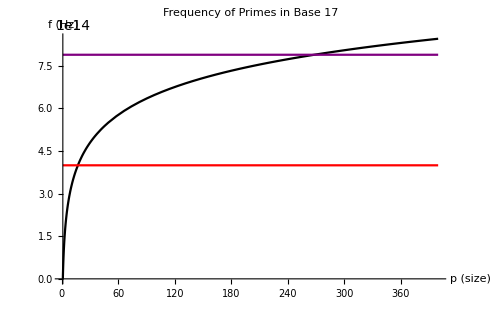

```mathematica
(* generate plot of freq. of each prime for a given base. include visibile range. *)
Plot[{f[p],fRED,fVIOLET},{p,1,400},PlotStyle->{Black,Red,Purple},AxesLabel->{"p (size)","f (Hz)"},PlotLabel->"Frequency of Primes in Base " <> ToString[base]]
```

```mathematica
(* Find the range of available primes/keys*)
pLow=Floor[Exp[Log[base]*fRED/f0]];
pHigh=Floor[Exp[Log[base]*fVIOLET/f0]];
primesInRange={};
Table[If[PrimeQ[n],AppendTo[primesInRange,n]],{n,pLow,pHigh}];
```

```mathematica
primesInRange
```

{11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113}

```mathematica
primeFreqs=Table[N[f[base,primesInRange[[i]]]],{i,1,Length[primesInRange]}]
```

{3.99733×10^14,4.27582×10^14,4.72302×10^14,4.90843×10^14,5.22692×10^14,5.61334×10^14,5.72452×10^14,6.01946×10^14,6.19059×10^14,6.26999×10^14,6.41826×10^14,6.61855×10^14,6.79733×10^14,6.8529×10^14,7.0093×10^14,7.10596×10^14,7.15227×10^14,7.28395×10^14,7.36628×10^14,7.48264×10^14,7.62612×10^14,7.69349×10^14,7.72617×10^14,7.78969×10^14,7.82056×10^14,7.88064×10^14}

```mathematica
Table[Style[primesInRange[[i]],Color[primesInRange[[i]]]],{i,1,Length[primesInRange]}]
```

{11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113}